# Homework #8

Problem 3: Find .

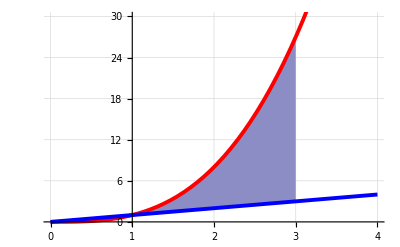

```mathematica
y1[x_]=x^3;
y2[x_]=x;
f[x_,y_]=x-y;
p1=Plot[{y1[x],y2[x]},{x,0,4},PlotTheme->"Scientific",PlotStyle->{{Red,Thickness[0.007]},{Blue,Thickness[0.007]}},GridLines->Automatic];
p2=Plot[{y1[x],y2[x]},{x,1,3},PlotStyle->{{Red,Thickness[0.002]},{Blue,Thickness[0.002]}},Filling->{1->{2}},ColorFunction->Function[{x,y},ColorData["TemperatureMap"][f[x,y]]],FillingStyle->Automatic,GridLines->Automatic];
Show[p2,p1,PlotRange->{{0,4},{0,30}}]
```

```mathematica
s=∫_1^3 ∫_y1[x]^y2[x] f[x,y]ⅆyⅆx;
Print["Value of this integral is ",N[s]]
```

Value of this integral is 112.076

Problem 6. Find .

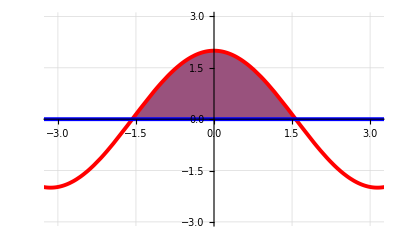

```mathematica
y1[ϕ_]=2Cos[ϕ];
y2[ϕ_]=0;
f[r_]=r^3;
p1=Plot[{y1[ϕ],y2[ϕ]},{ϕ,-2π,2π},PlotTheme->"Scientific",PlotStyle->{{Red,Thickness[0.007]},{Blue,Thickness[0.007]}},GridLines->Automatic];
p2=Plot[{y1[x],y2[x]},{x,-π/2,π/2},PlotStyle->{{Red,Thickness[0.002]},{Blue,Thickness[0.002]}},Filling->{1->{2}},ColorFunction->Function[{x,y},ColorData["TemperatureMap"][f[y]]],FillingStyle->Automatic,GridLines->Automatic];
Show[p2,p1,PlotRange->{{-π,π},{-3,3}}]
```

```mathematica
PolarPlot[2Cos[ϕ],{ϕ,-π/2,π/2},PlotTheme->"Business"]
```

-Graphics-

```mathematica
s=∫_(-π/2)^(π/2) ∫_y2[ϕ]^y1[ϕ] f[r]ⅆrⅆϕ;
Print["Value of this integral is ",s]
```

Value of this integral is (3 π)/2

Problem 8. Find .

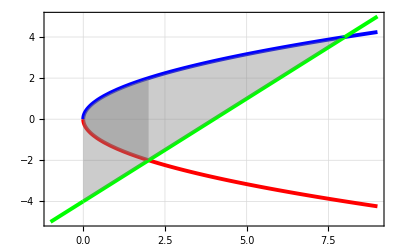

```mathematica
y1[x_]=-Sqrt[2x];
y2[x_]=Sqrt[2x];
y3[x_]=x-4;
p1=Plot[{y1[x],y2[x],y3[x]},{x,-1,9},PlotTheme->"Scientific",PlotStyle->{{Red,Thickness[0.007]},{Blue,Thickness[0.007]},{Green,Thickness[0.007]}},GridLines->Automatic];
p2=Plot[{y1[x],y2[x]},{x,0,2},PlotStyle->{{Red,Thickness[0.002]},{Blue,Thickness[0.002]}},Filling->{1->{2}},FillingStyle->Directive[Gray,Opacity[0.4]],GridLines->Automatic];
p3=Plot[{y3[x],y2[x]},{x,0,8},PlotStyle->{{Green,Thickness[0.002]},{Blue,Thickness[0.002]}},Filling->{1->{2}},FillingStyle->Directive[Gray,Opacity[0.4]],GridLines->Automatic];
Show[p1,p2,p3,PlotRange->{{-1,9},{-5,5}}]
```

```mathematica
s=∫_0^2 (∫_(-Sqrt[2x])^Sqrt[2x] yⅆy )xⅆx+∫_0^8 (∫_(x-4)^Sqrt[2x] yⅆy )xⅆx;
Print["Value of this integral is ",s]
```

Value of this integral is 256/3

Problem 10. Find

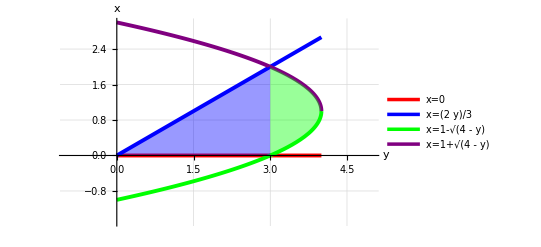

```mathematica
x1[y_]=(2y)/3;
x2[y_]=1-Sqrt[4-y];
x3[y_]=1+Sqrt[4-y];
p1=Plot[{0,x1[y],x2[y],x3[y]},{y,0,4},PlotStyle->{{Red,Thickness[0.007]},{Blue,Thickness[0.007]},{Green,Thickness[0.007]},{Purple,Thickness[0.007]}},GridLines->Automatic,PlotLegends->{"x=0","x=(2  y)/3","x=1-√(4 - y)","x=1+√(4 - y)"},AxesLabel->{y,x}];
p2=Plot[{x1[y]},{y,0,3},PlotStyle->{Blue,Thickness[0.002]},Filling->Axis,FillingStyle->Directive[Blue,Opacity[0.4]],GridLines->Automatic];
p3=Plot[{x2[y],x3[y]},{y,3,4},PlotStyle->{{Green,Thickness[0.002]},{Purple,Thickness[0.002]}},Filling->{1->{2}},FillingStyle->Directive[Green,Opacity[0.4]],GridLines->Automatic];
Show[p1,p2,p3,PlotRange->{{-1,5},{-1.5,3}}]
```

```mathematica
s=∫_0^3 (∫_0^((2y)/3) (x+y)ⅆx )ⅆy+∫_3^4 (∫_(1-Sqrt[4-y])^(1+Sqrt[4-y]) (x+y)ⅆx )ⅆy;
Print["Value of this integral is ",s]
```

Value of this integral is 208/15